## Logistic Map Bifurcations (by Iain Stewart)

```mathematica
?NestList
```

NestList[f,expr,n] gives a list of the results of applying f to expr 0 through n times.

```mathematica
(* Define a function to carryout the iterations of the map function f  on initial value x0 for parameter r.  Iterate nmax time and then drop nmin terms. *)
```

```mathematica
fMaplist[r_,x0_,nmin_,nmax_]:=Module[{ylst,ylstd},
ylst=NestList[f[r],x0,nmax]; (* make a list by iterating f[r][x], starting on x=x0, with nmax iterations *)
ylstd=Drop[ylst,nmin];   (* get rid of first nmin points, x_0 to x_{nmin-1} *)
Table[{r,ylstd[[i]]},{i,1,Length[ylstd]}]    (* output a list of {r,x_n} pairs for n≥nmin *)
]
```

```mathematica
(* same thing but do not output list with the r value *)
fMaplistnor[r_,x0_,nmin_,nmax_]:=Module[{ylst,ylstd},
ylst=NestList[f[r],x0,nmax]; (* make a list by iterating f[r][x], starting on x=x0, with nmax iterations *)
ylstd=Drop[ylst,nmin]   (* get rid of first nmin points, x_0 to x_{nmin-1} *)
]
```

```mathematica
(* Note we can define a mapping function f[r][x] without having to reinitialize the above fMaplist and fMaplistnor commands *)
```

```mathematica
(* Logistic Map *)
Clear[f]
f[r_][x_]:=r*x*(1-x);
```

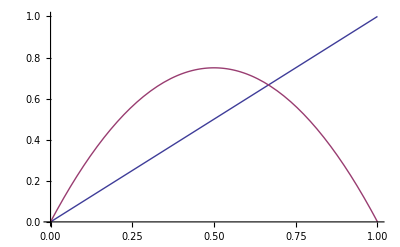

```mathematica
Plot[{x,f[3][x]},{x,0,1}]
```

```mathematica
(* output a few values to make sure everyting is working, here we use whatever the currently defined f is  *)
fMaplist[3.5,.1,2,5]
```

{{3.5,0.755213},{3.5,0.647033},{3.5,0.799335},{3.5,0.561396}}

```mathematica
fMaplistnor[3.5,.1,2,5]
```

{0.755213,0.647033,0.799335,0.561396}

```mathematica
?ListPlot
```

ListPlot[{y_1,y_2,…}] plots points corresponding to a list of values, assumed to correspond to x coordinates 1, 2, …. 
ListPlot[{{x_1,y_1},{x_2,y_2},…}] plots a list of points with specified x and y coordinates. 
ListPlot[{list_1,list_2,…}] plots several lists of points.

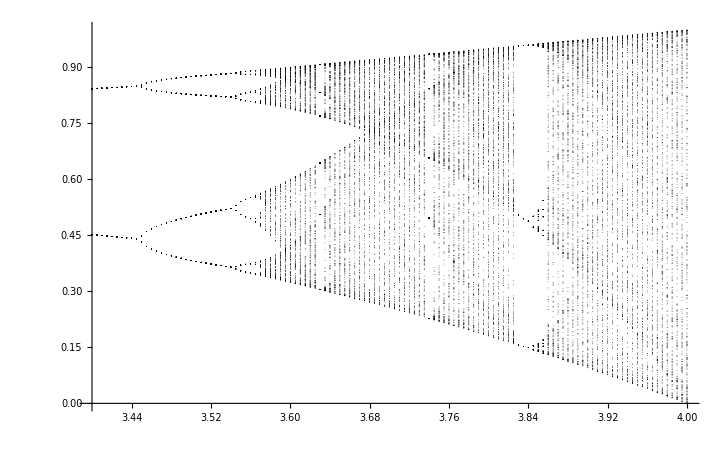

```mathematica
(* Low precision plot, ie use a lower density for r values which is quicker *)
ListPlot[Table[fMaplist[r,.1,300,600],{r,3.4,4.0,.005}],PlotStyle->{{Black,PointSize[.0005]}}]
```

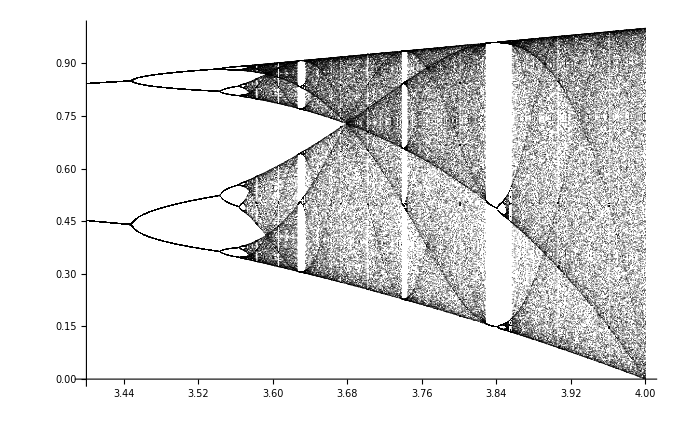

```mathematica
(* High precision *)
ListPlot[Table[fMaplist[r,.1,300,600],{r,3.4,4.0,.001}],PlotStyle->{{Black,PointSize[.0005]}}]
```

```mathematica
(* Plot to print *)
tmp=ListPlot[Table[fMaplist[r,.1,300,600],{r,2.9,4.0,.001}],PlotStyle->{{Black,PointSize[.001]}},AxesLabel->{"r","x"},
LabelStyle->18]
```

-Graphics-

```mathematica
Export["~/8.09/Logistic_Map.eps",tmp]
```

~/8.09/Logistic_Map.eps

```mathematica
Export["~/8.09/Logistic_Map.pdf",tmp]
```

~/8.09/Logistic_Map.pdf